```mathematica
(AA&&CC)||(AA&&DD)||(BB&&DD)||(BB&&EE)||(CC&&EE)//LogicalExpand
```

(AA&&CC)||(AA&&DD)||(BB&&DD)||(BB&&EE)||(CC&&EE)

```mathematica
Second[list_]:=First[Rest[list]]
```

```mathematica
QuadrilateralsWithPattern[6,1]
```

{{{1,3},{2,6},{4},{5}},{{1,3},{2},{4,6},{5}},{{1,3},{2},{4},{5,6}},{{1,3,6},{2},{4},{5}}}

```mathematica
Clear[ShowForNodesFull2];ShowForNodesFull2[nodes_]:=Block[{done=0},
Monitor[
Flatten[
Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]]
},
done++;
{Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],{part1,part2,part3,part4,part5}}
],
{part1,QuadrilateralsWithPattern[nodes,1]},
{part2,QuadrilateralsWithPattern[nodes,2]},
{part3,QuadrilateralsWithPattern[nodes,3]},
{part4,QuadrilateralsWithPattern[nodes,4]},
{part5,QuadrilateralsWithPattern[nodes,5]}
],
4],
done
]]
```

```mathematica
all=ShowForNodesFull2[6];
```

```mathematica
SHowSol2[sol_]:=Block[
{
start = Select[sol[[1]],MemberQ[sol[[2]],SymbolToSets[#]]&],
other = Select[sol[[1]],!MemberQ[sol[[2]],SymbolToSets[#]]&]
},
ShowGraphs[start,Directive[Dotted,Thick,Orange]&]->
ShowGraphs[other,If[HasQuadrilateralPattern[#],Red,Darker[Green]]&]
]
```

```mathematica
SHowSol3[sol_]:=Block[
{
start = Select[sol[[1]],MemberQ[sol[[2]],SymbolToSets[#]]&],
other =Map[SymbolToSets, Select[sol[[1]],!MemberQ[sol[[2]],SymbolToSets[#]]&]]
},
{Length[Select[other,HasQuadrilateralPattern]],Length[Select[other,HasTrianglePattern]]}->start
]
```

```mathematica
Map[First,Map[SHowSol3,all]]//Tally//Sort
```

{{{1,5},10},{{2,5},20},{{5,5},120},{{6,5},190},{{10,5},505},{{15,5},179}}

```mathematica
all7=ShowForNodesFull2[7];
```

$Aborted

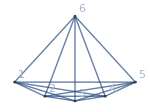
{{-Graphics-16♁35,-Graphics-16♁25,-Graphics-16♁24,-Graphics-14♁26,-Graphics-13♁26}→{-Graphics-26♁35,-Graphics-24♁35,-Graphics-14♁35,-Graphics-14♁25,-Graphics-13♁25,-Graphics-13♁24}}

```mathematica
ShowSols[6,First]
```

```mathematica
ShowSols[6,First[Take[#,{4,4}]]&]
```

{{-Graphics-356,-Graphics-256,-Graphics-246,-Graphics-146,-Graphics-136}→{-Graphics-35♁46,-Graphics-26♁35,-Graphics-25♁46,-Graphics-25♁36,-Graphics-24♁56,-Graphics-24♁36,-Graphics-24♁35,-Graphics-16♁35,-Graphics-16♁25,-Graphics-16♁24,-Graphics-14♁56,-Graphics-14♁36,-Graphics-14♁35,-Graphics-14♁26,-Graphics-14♁25,-Graphics-13♁56,-Graphics-13♁46,-Graphics-13♁26,-Graphics-13♁25,-Graphics-13♁24}}

```mathematica
ShowForNodesFull[6,First]
```

{{v1x26x35x4,v1x24x35x6,v16x2x35x4,v16x25x3x4,v16x24x3x5,v14x2x35x6,v14x26x3x5,v14x25x3x6,v13x26x4x5,v13x25x4x6,v13x24x5x6},{{{1,3},{2,6},{4},{5}},{{1,6},{2,4},{3},{5}},{{1,6},{2},{3,5},{4}},{{1,4},{2,6},{3},{5}},{{1,6},{2,5},{3},{4}}}}

```mathematica
kids={"lena","elien","caroline","kaat","xari","leontien","louise","sofia","fiebe","kayleigh","willy"}
```

{lena,elien,caroline,kaat,xari,leontien,louise,sofia,fiebe,kayleigh,willy}

```mathematica
DamerauLevenshteinDistance["abc","cba"]
```

2

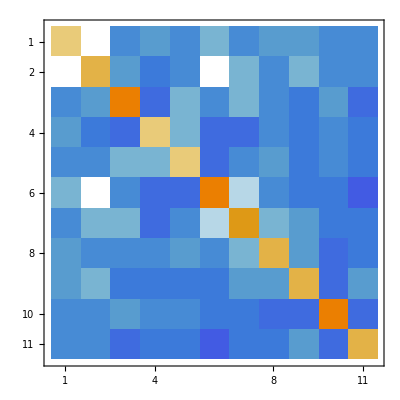

```mathematica
Table[Levens[first,second],{first,kids},{second,kids}]//MatrixPlot
```

```mathematica
Table[NeedlemanWunschSimilarity[first,second],{first,kids},{second,kids}]//MatrixForm
```

(4. | 0. | -4. | -3. | -4. | -2. | -4. | -3. | -3. | -4. | -4.
0. | 5. | -3. | -5. | -4. | 0. | -2. | -4. | -2. | -4. | -4.
-4. | -3. | 8. | -6. | -2. | -4. | -2. | -4. | -5. | -3. | -6.
-3. | -5. | -6. | 4. | -2. | -6. | -6. | -4. | -5. | -4. | -5.
-4. | -4. | -2. | -2. | 4. | -6. | -4. | -3. | -5. | -4. | -5.
-2. | 0. | -4. | -6. | -6. | 8. | -1. | -4. | -5. | -5. | -7.
-4. | -2. | -2. | -6. | -4. | -1. | 6. | -2. | -3. | -5. | -5.
-3. | -4. | -4. | -4. | -3. | -4. | -2. | 5. | -3. | -6. | -5.
-3. | -2. | -5. | -5. | -5. | -5. | -3. | -3. | 5. | -6. | -3.
-4. | -4. | -3. | -4. | -4. | -5. | -5. | -6. | -6. | 8. | -6.
-4. | -4. | -6. | -5. | -5. | -7. | -5. | -5. | -3. | -6. | 5.)